```mathematica
tnw=NotebookOpen[SetDirectory[NotebookDirectory[]]<>"/ThesisNoWOrries.nb",Visible->False];
SelectionMove[tnw,All,Notebook];
SelectionEvaluate[tnw];
```

```mathematica
(* Example 1 *)
```

```mathematica
data=Select[Import["test1.xlsx"][[1]],#[[-1]]≠""&][[2;;-1]];
X=data[[All,8;;29]];
M=data[[All,31;;40]];
Dem=data[[All,2;;7]];
DemName=Import["test1.xlsx"][[1,1,2;;7]];
semmethod=If[1==Times@@(Boole[BaringhausHenzeTest[#,"TestDataTable"][[1,1,2,-1]]>0.05]&/@{X,M}),"ML","ULS"];
```

所有報表請選取後按滑鼠右鍵->選擇Copy As Plain Text->開啟Excel貼上

次數分配

人口變項 | 組別 | 次數 | 百分比
性別 | 女 | 7 | 13.21%
 | 男 | 46 | 86.79%
階級 | WA1 | 12 | 22.64%
 | WA2 | 26 | 49.06%
 | WA3 | 15 | 28.30%
學歷 | 專科 | 9 | 16.98%
 | 大學（含二技） | 15 | 28.30%
 | 高中職（含以下) | 29 | 54.72%
年齡 | 25 歲以下 | 22 | 41.51%
 | 26~30 歲 | 13 | 24.53%
 | 31-40 歲 | 16 | 30.19%
 | 40 歲以上 | 2 | 3.77%
年資 | 11~15年 | 11 | 20.75%
 | 16～20年 | 6 | 11.32%
 | 5年以下 | 26 | 49.06%
 | 6~10年 | 10 | 18.87%
婚姻狀況 | 已婚 | 15 | 28.30%
 | 未婚 | 38 | 71.70%

項目分析

項目分析-X

題項 | 組別 | 個數 | 平均數 | 標準差 | CR | P-Vale | 與分量表總分相關係數 | 與非該題項總分相關係數 | 與總分相關係數
V01 | 低分組 | 15 | 3.6667 | 0.8997 | -6.9690 | 0.0000 | 0.801 | 0.661 | 0.692
 | 高分組 | 15 | 5.5333 | 0.5164 |  |  |  |  | 
V02 | 低分組 | 15 | 4.2000 | 0.8619 | -5.6745 | 0.0000 | 0.817 | 0.683 | 0.708
 | 高分組 | 15 | 5.7333 | 0.5936 |  |  |  |  | 
V03 | 低分組 | 15 | 4.0000 | 0.8452 | -6.0810 | 0.0000 | 0.783 | 0.621 | 0.658
 | 高分組 | 15 | 5.8000 | 0.7746 |  |  |  |  | 
V04 | 低分組 | 15 | 3.7333 | 0.5936 | -10.3330 | 0.0000 | 0.875 | 0.803 | 0.821
 | 高分組 | 15 | 5.7333 | 0.4577 |  |  |  |  | 
V05 | 低分組 | 15 | 3.9333 | 0.7988 | -9.2269 | 0.0000 | 0.870 | 0.829 | 0.844
 | 高分組 | 15 | 5.9333 | 0.2582 |  |  |  |  | 
V06 | 低分組 | 15 | 3.8000 | 0.5606 | -9.7701 | 0.0000 | 0.823 | 0.768 | 0.789
 | 高分組 | 15 | 5.8000 | 0.5606 |  |  |  |  | 
V07 | 低分組 | 15 | 3.7333 | 0.7037 | -7.9993 | 0.0000 | 0.809 | 0.729 | 0.757
 | 高分組 | 15 | 5.6667 | 0.6172 |  |  |  |  | 
V08 | 低分組 | 15 | 3.3333 | 0.8997 | -9.6457 | 0.0000 | 0.892 | 0.759 | 0.788
 | 高分組 | 15 | 5.8000 | 0.4140 |  |  |  |  | 
V09 | 低分組 | 15 | 3.2000 | 0.5606 | -5.5297 | 0.0000 | 0.869 | 0.673 | 0.709
 | 高分組 | 15 | 5.2667 | 1.3345 |  |  |  |  | 
V10 | 低分組 | 15 | 3.2667 | 0.8837 | -8.0459 | 0.0000 | 0.874 | 0.775 | 0.799
 | 高分組 | 15 | 5.5333 | 0.6399 |  |  |  |  | 
V11 | 低分組 | 15 | 3.4000 | 0.6325 | -8.4664 | 0.0000 | 0.840 | 0.684 | 0.717
 | 高分組 | 15 | 5.5333 | 0.7432 |  |  |  |  | 
V12 | 低分組 | 15 | 3.4000 | 0.7368 | -9.5511 | 0.0000 | 0.857 | 0.747 | 0.773
 | 高分組 | 15 | 5.7333 | 0.5936 |  |  |  |  | 
V13 | 低分組 | 15 | 3.4000 | 0.8281 | -7.6872 | 0.0000 | 0.813 | 0.797 | 0.818
 | 高分組 | 15 | 5.6000 | 0.7368 |  |  |  |  | 
V14 | 低分組 | 15 | 3.3333 | 0.7237 | -6.5552 | 0.0000 | 0.783 | 0.741 | 0.767
 | 高分組 | 15 | 5.2667 | 0.8837 |  |  |  |  | 
V15 | 低分組 | 15 | 3.3333 | 0.6172 | -8.1435 | 0.0000 | 0.890 | 0.726 | 0.754
 | 高分組 | 15 | 5.3333 | 0.7237 |  |  |  |  | 
V16 | 低分組 | 15 | 3.4667 | 1.0601 | -5.1729 | 0.0000 | 0.624 | 0.640 | 0.677
 | 高分組 | 15 | 5.4000 | 0.9856 |  |  |  |  | 
V17 | 低分組 | 15 | 3.5333 | 0.6399 | -12.3740 | 0.0000 | 0.846 | 0.802 | 0.823
 | 高分組 | 15 | 5.8667 | 0.3519 |  |  |  |  | 
V18 | 低分組 | 15 | 3.2667 | 0.9612 | -6.4191 | 0.0000 | 0.881 | 0.657 | 0.698
 | 高分組 | 15 | 5.4667 | 0.9155 |  |  |  |  | 
V19 | 低分組 | 15 | 3.6000 | 1.0556 | -6.2538 | 0.0000 | 0.904 | 0.751 | 0.777
 | 高分組 | 15 | 5.6667 | 0.7237 |  |  |  |  | 
V20 | 低分組 | 15 | 3.7333 | 1.0998 | -6.4841 | 0.0000 | 0.906 | 0.784 | 0.806
 | 高分組 | 15 | 5.8000 | 0.5606 |  |  |  |  | 
V21 | 低分組 | 15 | 3.2667 | 1.0328 | -7.3704 | 0.0000 | 0.928 | 0.812 | 0.833
 | 高分組 | 15 | 5.6667 | 0.7237 |  |  |  |  | 
V22 | 低分組 | 15 | 3.4667 | 1.1872 | -2.8280 | 0.0086 | 0.682 | 0.412 | 0.477
 | 高分組 | 15 | 5.0000 | 1.7321 |  |  |  |  |

項目分析-M

題項 | 組別 | 個數 | 平均數 | 標準差 | CR | P-Vale | 與分量表總分相關係數 | 與非該題項總分相關係數 | 與總分相關係數
V01 | 低分組 | 15 | 2.0000 | 1.0690 | -13.4110 | 0.0000 | 0.912 | 0.790 | 0.842
 | 高分組 | 16 | 5.8750 | 0.3416 |  |  |  |  | 
V02 | 低分組 | 15 | 1.5333 | 0.6399 | -19.2850 | 0.0000 | 0.900 | 0.899 | 0.924
 | 高分組 | 16 | 5.7500 | 0.5774 |  |  |  |  | 
V03 | 低分組 | 15 | 1.8000 | 0.7746 | -13.6900 | 0.0000 | 0.903 | 0.823 | 0.864
 | 高分組 | 16 | 5.5000 | 0.7303 |  |  |  |  | 
V04 | 低分組 | 15 | 1.4667 | 0.5164 | -14.8830 | 0.0000 | 0.939 | 0.889 | 0.915
 | 高分組 | 16 | 5.3750 | 0.8851 |  |  |  |  | 
V05 | 低分組 | 15 | 3.5333 | 1.5976 | -4.9058 | 0.0001 | 0.733 | 0.593 | 0.659
 | 高分組 | 16 | 5.6875 | 0.6021 |  |  |  |  | 
V06 | 低分組 | 15 | 1.8000 | 0.8619 | -13.9480 | 0.0000 | 0.898 | 0.907 | 0.927
 | 高分組 | 16 | 5.5625 | 0.6292 |  |  |  |  | 
V07 | 低分組 | 15 | 1.3333 | 0.4880 | -15.7070 | 0.0000 | 0.887 | 0.873 | 0.902
 | 高分組 | 16 | 5.1250 | 0.8062 |  |  |  |  | 
V08 | 低分組 | 15 | 3.4000 | 1.9198 | -1.4233 | 0.1653 | 0.416 | 0.169 | 0.285
 | 高分組 | 16 | 4.3750 | 1.8930 |  |  |  |  | 
V09 | 低分組 | 15 | 1.5333 | 0.6399 | -11.2190 | 0.0000 | 0.916 | 0.861 | 0.890
 | 高分組 | 16 | 4.9375 | 0.9979 |  |  |  |  | 
V10 | 低分組 | 15 | 2.5333 | 1.5523 | -4.5494 | 0.0001 | 0.772 | 0.559 | 0.634
 | 高分組 | 16 | 4.8750 | 1.3102 |  |  |  |  |

信度分析

各分量表 | Cronbach'α | 整體信度
X1 | 0.881 | 0.960
X2 | 0.905 | 
X3 | 0.893 | 
X4 | 0.916 | 
M1 | 0.927 | 0.933
M2 | 0.838 |

一階CFA模式配適度

一階CFA-X

模式配適度指標 | 
卡方值 | 231.403
自由度 | 203.000
P-value | If[Abs[Missing[]]<0.000,0.000,Missing[]]
卡方值/自由度 | 1.140
CFI | 0.995
NFI | 0.964
RMSEA | 0.052
GFI | 0.973
AGFI | 0.967

聚合效度 (AVE) 與收斂信度 (CR)

題項 | 因素負荷 | P-value | AVE | CR
V01 | 0.721 |  | 0.617 | 0.888
V02 | 0.738 | 0.000 |  | 
V03 | 0.675 | 0.000 |  | 
V04 | 0.87 | 0.000 |  | 
V05 | 0.9 | 0.000 |  | 
V06 | 0.828 |  | 0.670 | 0.910
V07 | 0.809 | 0.000 |  | 
V08 | 0.851 | 0.000 |  | 
V09 | 0.748 | 0.000 |  | 
V10 | 0.851 | 0.000 |  | 
V11 | 0.743 |  | 0.626 | 0.893
V12 | 0.797 | 0.000 |  | 
V13 | 0.849 | 0.000 |  | 
V14 | 0.78 | 0.000 |  | 
V15 | 0.783 | 0.000 |  | 
V16 | 0.704 |  | 0.660 | 0.929
V17 | 0.914 | 0.000 |  | 
V18 | 0.766 | 0.000 |  | 
V19 | 0.873 | 0.000 |  | 
V20 | 0.909 | 0.000 |  | 
V21 | 0.937 | 0.000 |  | 
V22 | 0.488 | 0.000 |  |

區隔效度

| X1 | X2 | X3 | X4
X1 | 0.786 |  |  | 
X2 | 0.616 | 0.818 |  | 
X3 | 0.615 | 0.743 | 0.791 | 
X4 | 0.495 | 0.397 | 0.465 | 0.813

一階CFA-M

模式配適度指標 | 
卡方值 | 45.390
自由度 | 34.000
P-value | If[Abs[Missing[]]<0.000,0.000,Missing[]]
卡方值/自由度 | 1.335
CFI | 0.999
NFI | 0.994
RMSEA | 0.080
GFI | 0.996
AGFI | 0.994

聚合效度 (AVE) 與收斂信度 (CR)

題項 | 因素負荷 | P-value | AVE | CR
V01 | 0.84 |  | 0.727 | 0.929
V02 | 0.939 | 0.000 |  | 
V03 | 0.875 | 0.000 |  | 
V04 | 0.937 | 0.000 |  | 
V05 | 0.634 | 0.000 |  | 
V06 | 0.974 |  | 0.607 | 0.868
V07 | 0.94 | 0.000 |  | 
V08 | 0.178 | 0.000 |  | 
V09 | 0.902 | 0.000 |  | 
V10 | 0.597 | 0.000 |  |

區隔效度

| M1 | M2
M1 | 0.852 | 
M2 | 0.646 | 0.779

變異數分析

人口統計變數 | 因素 | 組別 | 平均數 | 標準差 | F值 | P 值 | 事後比較
性別 | X1 | 女 | 5.057 | 1.242 | 0.754 | 0.389 | 
 |  | 男 | 4.765 | 0.757 |  |  | 
 | X2 | 女 | 4.971 | 1.319 | 0.814 | 0.371 | 
 |  | 男 | 4.604 | 0.953 |  |  | 
 | X3 | 女 | 4.800 | 1.301 | 0.574 | 0.452 | 
 |  | 男 | 4.504 | 0.907 |  |  | 
 | X4 | 女 | 4.980 | 1.225 | 1.298 | 0.260 | 
 |  | 男 | 4.509 | 0.986 |  |  | 
 | X整體 | 女 | 4.955 | 1.258 | 1.118 | 0.295 | 
 |  | 男 | 4.588 | 0.785 |  |  | 
 | M1 | 女 | 4.343 | 1.700 | 0.857 | 0.359 | 
 |  | 男 | 3.761 | 1.529 |  |  | 
 | M2 | 女 | 3.829 | 1.849 | 0.112 | 0.740 | 
 |  | 男 | 3.657 | 1.171 |  |  | 
 | M整體 | 女 | 4.086 | 1.734 | 0.481 | 0.491 | 
 |  | 男 | 3.709 | 1.279 |  |  | 
階級 | X1 | WA1 | 4.867 | 0.462 | 2.588 | 0.085 | 
 |  | WA2 | 5.000 | 0.862 |  |  | 
 |  | WA3 | 4.413 | 0.899 |  |  | 
 | X2 | WA1 | 5.100 | 0.543 | 5.154 | 0.009 | WA1--WA3
 |  | WA2 | 4.808 | 0.966 |  |  | WA2--WA3
 |  | WA3 | 4.027 | 1.090 |  |  | 
 | X3 | WA1 | 5.017 | 0.455 | 7.833 | 0.001 | WA1--WA3
 |  | WA2 | 4.738 | 0.917 |  |  | WA2--WA3
 |  | WA3 | 3.827 | 0.965 |  |  | 
 | X4 | WA1 | 4.786 | 0.727 | 2.307 | 0.110 | 
 |  | WA2 | 4.742 | 1.018 |  |  | 
 |  | WA3 | 4.105 | 1.128 |  |  | 
 | X整體 | WA1 | 4.928 | 0.382 | 4.924 | 0.011 | WA1--WA3
 |  | WA2 | 4.815 | 0.817 |  |  | WA2--WA3
 |  | WA3 | 4.094 | 0.982 |  |  | 
 | M1 | WA1 | 4.133 | 1.580 | 1.040 | 0.361 | 
 |  | WA2 | 3.977 | 1.670 |  |  | 
 |  | WA3 | 3.360 | 1.265 |  |  | 
 | M2 | WA1 | 3.583 | 1.018 | 2.044 | 0.140 | 
 |  | WA2 | 4.000 | 1.232 |  |  | 
 |  | WA3 | 3.200 | 1.386 |  |  | 
 | M整體 | WA1 | 3.858 | 1.259 | 1.408 | 0.254 | 
 |  | WA2 | 3.988 | 1.362 |  |  | 
 |  | WA3 | 3.280 | 1.302 |  |  | 
學歷 | X1 | 專科 | 4.800 | 0.510 | 0.215 | 0.807 | 
 |  | 大學（含二技） | 4.920 | 0.736 |  |  | 
 |  | 高中職（含以下) | 4.745 | 0.956 |  |  | 
 | X2 | 專科 | 4.756 | 0.767 | 5.155 | 0.009 | 大學（含二技）--高中職（含以下)
 |  | 大學（含二技） | 5.253 | 0.644 |  |  | 
 |  | 高中職（含以下) | 4.310 | 1.080 |  |  | 
 | X3 | 專科 | 4.556 | 0.546 | 3.798 | 0.029 | 大學（含二技）--高中職（含以下)
 |  | 大學（含二技） | 5.067 | 0.617 |  |  | 
 |  | 高中職（含以下) | 4.269 | 1.097 |  |  | 
 | X4 | 專科 | 4.175 | 0.772 | 2.502 | 0.092 | 
 |  | 大學（含二技） | 5.029 | 0.773 |  |  | 
 |  | 高中職（含以下) | 4.458 | 1.135 |  |  | 
 | X整體 | 專科 | 4.535 | 0.426 | 2.833 | 0.068 | 
 |  | 大學（含二技） | 5.064 | 0.614 |  |  | 
 |  | 高中職（含以下) | 4.447 | 0.990 |  |  | 
 | M1 | 專科 | 3.800 | 1.800 | 0.257 | 0.774 | 
 |  | 大學（含二技） | 4.080 | 1.702 |  |  | 
 |  | 高中職（含以下) | 3.724 | 1.425 |  |  | 
 | M2 | 專科 | 3.822 | 0.777 | 0.339 | 0.714 | 
 |  | 大學（含二技） | 3.453 | 1.328 |  |  | 
 |  | 高中職（含以下) | 3.752 | 1.360 |  |  | 
 | M整體 | 專科 | 3.811 | 1.236 | 0.010 | 0.990 | 
 |  | 大學（含二技） | 3.767 | 1.461 |  |  | 
 |  | 高中職（含以下) | 3.738 | 1.340 |  |  | 
年齡 | X1 | 25 歲以下 | 4.664 | 0.822 | 0.489 | 0.691 | 
 |  | 26~30 歲 | 4.985 | 0.995 |  |  | 
 |  | 31-40 歲 | 4.813 | 0.743 |  |  | 
 |  | 40 歲以上 | 5.100 | 0.424 |  |  | 
 | X2 | 25 歲以下 | 4.345 | 1.084 | 1.468 | 0.235 | 
 |  | 26~30 歲 | 5.046 | 0.967 |  |  | 
 |  | 31-40 歲 | 4.725 | 0.885 |  |  | 
 |  | 40 歲以上 | 4.900 | 0.424 |  |  | 
 | X3 | 25 歲以下 | 4.145 | 1.016 | 2.870 | 0.046 | 25 歲以下--26~30 歲
 |  | 26~30 歲 | 5.031 | 0.966 |  |  | 
 |  | 31-40 歲 | 4.638 | 0.713 |  |  | 
 |  | 40 歲以上 | 5.000 | 0.283 |  |  | 
 | X4 | 25 歲以下 | 4.383 | 1.141 | 0.534 | 0.661 | 
 |  | 26~30 歲 | 4.747 | 1.085 |  |  | 
 |  | 31-40 歲 | 4.723 | 0.827 |  |  | 
 |  | 40 歲以上 | 4.286 | 0.808 |  |  | 
 | X整體 | 25 歲以下 | 4.384 | 0.952 | 1.251 | 0.301 | 
 |  | 26~30 歲 | 4.934 | 0.926 |  |  | 
 |  | 31-40 歲 | 4.724 | 0.627 |  |  | 
 |  | 40 歲以上 | 4.773 | 0.321 |  |  | 
 | M1 | 25 歲以下 | 3.255 | 1.619 | 2.684 | 0.057 | 
 |  | 26~30 歲 | 4.462 | 1.554 |  |  | 
 |  | 31-40 歲 | 3.938 | 1.237 |  |  | 
 |  | 40 歲以上 | 5.400 | 0.000 |  |  | 
 | M2 | 25 歲以下 | 3.264 | 1.285 | 1.665 | 0.187 | 
 |  | 26~30 歲 | 3.923 | 1.599 |  |  | 
 |  | 31-40 歲 | 3.925 | 0.772 |  |  | 
 |  | 40 歲以上 | 4.700 | 0.707 |  |  | 
 | M整體 | 25 歲以下 | 3.259 | 1.385 | 2.377 | 0.081 | 
 |  | 26~30 歲 | 4.192 | 1.541 |  |  | 
 |  | 31-40 歲 | 3.931 | 0.887 |  |  | 
 |  | 40 歲以上 | 5.050 | 0.354 |  |  | 
年資 | X1 | 11~15年 | 4.691 | 0.641 | 1.886 | 0.144 | 
 |  | 16～20年 | 5.433 | 0.543 |  |  | 
 |  | 5年以下 | 4.631 | 0.939 |  |  | 
 |  | 6~10年 | 5.000 | 0.686 |  |  | 
 | X2 | 11~15年 | 4.618 | 0.761 | 1.608 | 0.200 | 
 |  | 16～20年 | 5.233 | 0.731 |  |  | 
 |  | 5年以下 | 4.408 | 1.202 |  |  | 
 |  | 6~10年 | 4.980 | 0.561 |  |  | 
 | X3 | 11~15年 | 4.727 | 0.700 | 1.722 | 0.175 | 
 |  | 16～20年 | 5.067 | 0.242 |  |  | 
 |  | 5年以下 | 4.262 | 1.155 |  |  | 
 |  | 6~10年 | 4.760 | 0.717 |  |  | 
 | X4 | 11~15年 | 4.701 | 0.819 | 0.651 | 0.586 | 
 |  | 16～20年 | 4.833 | 0.696 |  |  | 
 |  | 5年以下 | 4.374 | 1.179 |  |  | 
 |  | 6~10年 | 4.786 | 0.953 |  |  | 
 | X整體 | 11~15年 | 4.686 | 0.414 | 1.517 | 0.222 | 
 |  | 16～20年 | 5.114 | 0.489 |  |  | 
 |  | 5年以下 | 4.414 | 1.072 |  |  | 
 |  | 6~10年 | 4.873 | 0.596 |  |  | 
 | M1 | 11~15年 | 3.945 | 1.333 | 1.440 | 0.242 | 
 |  | 16～20年 | 5.000 | 0.963 |  |  | 
 |  | 5年以下 | 3.600 | 1.664 |  |  | 
 |  | 6~10年 | 3.640 | 1.594 |  |  | 
 | M2 | 11~15年 | 3.727 | 0.647 | 2.444 | 0.075 | 
 |  | 16～20年 | 4.900 | 0.374 |  |  | 
 |  | 5年以下 | 3.438 | 1.418 |  |  | 
 |  | 6~10年 | 3.520 | 1.357 |  |  | 
 | M整體 | 11~15年 | 3.836 | 0.880 | 2.068 | 0.117 | 
 |  | 16～20年 | 4.950 | 0.517 |  |  | 
 |  | 5年以下 | 3.519 | 1.487 |  |  | 
 |  | 6~10年 | 3.580 | 1.404 |  |  | 
婚姻狀況 | X1 | 已婚 | 4.813 | 0.746 | 0.003 | 0.958 | 
 |  | 未婚 | 4.800 | 0.866 |  |  | 
 | X2 | 已婚 | 4.733 | 0.949 | 0.133 | 0.717 | 
 |  | 未婚 | 4.621 | 1.031 |  |  | 
 | X3 | 已婚 | 4.733 | 0.864 | 0.820 | 0.370 | 
 |  | 未婚 | 4.468 | 0.993 |  |  | 
 | X4 | 已婚 | 4.724 | 0.761 | 0.462 | 0.500 | 
 |  | 未婚 | 4.511 | 1.109 |  |  | 
 | X整體 | 已婚 | 4.748 | 0.621 | 0.355 | 0.554 | 
 |  | 未婚 | 4.592 | 0.936 |  |  | 
 | M1 | 已婚 | 3.893 | 1.452 | 0.026 | 0.871 | 
 |  | 未婚 | 3.816 | 1.602 |  |  | 
 | M2 | 已婚 | 3.893 | 0.953 | 0.600 | 0.442 | 
 |  | 未婚 | 3.595 | 1.363 |  |  | 
 | M整體 | 已婚 | 3.893 | 1.100 | 0.211 | 0.648 | 
 |  | 未婚 | 3.705 | 1.425 |  |  |

階層回歸

相關分析

 | X1 | X2 | X3 | X4 | M1 | M2
X1 | 1.000* | 0.785* | 0.784* | 0.703* | 0.621* | 0.662*
X2 | 0.785* | 1.000* | 0.862* | 0.630* | 0.529* | 0.489*
X3 | 0.784* | 0.862* | 1.000* | 0.682* | 0.510* | 0.561*
X4 | 0.703* | 0.630* | 0.682* | 1.000* | 0.491* | 0.515*
M1 | 0.621* | 0.529* | 0.510* | 0.491* | 1.000* | 0.804*
M2 | 0.662* | 0.489* | 0.561* | 0.515* | 0.804* | 1.000*

階層迴歸分析

 | M1 |  | M2 | 
變數 | 估計值 | P 值 | 估計值 | P 值
X1 | 0.923 | 0.021 | 0.937 | 0.003
X2 | 0.185 | 0.615 | -0.320 | 0.259
X3 | -0.080 | 0.840 | 0.326 | 0.284
X4 | 0.156 | 0.538 | 0.090 | 0.641
R^2 | 0.395 |  | 0.460 | 
Adj_R^2 | 0.344 |  | 0.415 | 
F | 7.826 |  | 10.218 | 
P value | 0.000 |  | 0.000 |

SEM結構方程式模式

各概念平均數及標準差

概念 | 平均數 | 標準差
X1 | 4.804 | 0.827
X2 | 4.653 | 1.001
X3 | 4.543 | 0.958
X4 | 4.571 | 1.020
M1 | 3.838 | 1.548
M2 | 3.679 | 1.259

模式配適度

模式配適度指標 | 
卡方值 | 1.493
自由度 | 8.000
P-value | Missing[]
卡方值/自由度 | 0.187
CFI | 1.000
NFI | 0.997
RMSEA | 0.000
GFI | 0.999
AGFI | 0.996

模式配適度Modification Indices值

{}

測量模式與結構模式檢定彙整表

路徑 | 標準化路徑係數 | P-value
XX→X1 | 0.954 | 
XX→X2 | 0.850 | 0.000
XX→X3 | 0.882 | 0.000
XX→X4 | 0.771 | 0.000
MM→M1 | 0.883 | 
MM→M2 | 0.911 | 0.000
XX→MM | 0.703 | 0.000

研究架構路徑圖

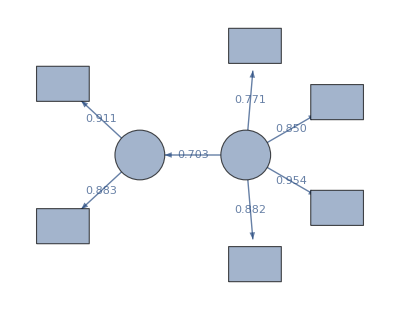

Null

```mathematica
ThesisNoWorryXM[X,M,{5,5,5,7},{5,5},{X1,X2,X3,X4},{M1,M2},Dem,DemName,""]
```

```mathematica
(* Example 2 *)
```

```mathematica
data=Select[Import["test2.xlsx"][[1]],#[[-1]]≠""&][[2;;-1]];
X=data[[All,1;;12]];
M=data[[All,13;;18]];
Y=data[[All,19;;24]];
Dem=data[[All,25;;25]];
DemName={"性別"};
semmethod=If[1==Times@@(Boole[BaringhausHenzeTest[#,"TestDataTable"][[1,1,2,-1]]>0.05]&/@{X,M,Y}),"ML","ULS"];
```

```mathematica
thesisnoworryanova[X,M,Y,{3,3,3,3},{3,3},{3,3},{X1,X2,X3,X4},{M1,M2},{Y1,Y2},Dem,DemName]
```

人口統計變數 | 因素 | 組別 | 平均數 | 標準差 | F值 | P 值 | 事後比較
性別 | X1 | 女 | 3.863 | 0.878 | 10.043 | 0.002 | 女--男
 |  | 男 | 4.247 | 0.557 |  |  | 
 | X2 | 女 | 4.140 | 0.669 | 7.784 | 0.006 | 女--男
 |  | 男 | 4.402 | 0.510 |  |  | 
 | X3 | 女 | 3.297 | 0.793 | 3.185 | 0.075 | 
 |  | 男 | 3.500 | 0.693 |  |  | 
 | X4 | 女 | 3.557 | 0.753 | 2.918 | 0.089 | 
 |  | 男 | 3.747 | 0.763 |  |  | 
 | X整體 | 女 | 3.714 | 0.652 | 7.983 | 0.005 | 女--男
 |  | 男 | 3.974 | 0.506 |  |  | 
 | M1 | 女 | 3.594 | 0.816 | 6.337 | 0.012 | 女--男
 |  | 男 | 3.885 | 0.657 |  |  | 
 | M2 | 女 | 3.428 | 0.857 | 6.835 | 0.009 | 女--男
 |  | 男 | 3.747 | 0.715 |  |  | 
 | M整體 | 女 | 3.511 | 0.779 | 7.583 | 0.006 | 女--男
 |  | 男 | 3.816 | 0.643 |  |  | 
 | Y1 | 女 | 3.620 | 0.656 | 6.751 | 0.010 | 女--男
 |  | 男 | 3.862 | 0.534 |  |  | 
 | Y2 | 女 | 3.664 | 0.928 | 5.755 | 0.017 | 女--男
 |  | 男 | 3.971 | 0.597 |  |  | 
 | Y整體 | 女 | 3.642 | 0.733 | 7.280 | 0.007 | 女--男
 |  | 男 | 3.917 | 0.499 |  |  |

所有報表請選取後按滑鼠右鍵->選擇Copy As Plain Text->開啟Excel貼上

次數分配

人口變項 | 組別 | 次數 | 百分比
性別 | 女 | 229 | 79.79%
 | 男 | 58 | 20.21%

項目分析

項目分析-X

題項 | 組別 | 個數 | 平均數 | 標準差 | CR | P-Vale | 與分量表總分相關係數 | 與非該題項總分相關係數 | 與總分相關係數
V01 | 低分組 | 79 | 2.9494 | 0.7663 | -18.1410 | 0.0000 | 0.909 | 0.813 | 0.851
 | 高分組 | 84 | 4.7738 | 0.4747 |  |  |  |  | 
V02 | 低分組 | 79 | 2.8354 | 1.0911 | -14.3130 | 0.0000 | 0.929 | 0.676 | 0.749
 | 高分組 | 84 | 4.7619 | 0.5058 |  |  |  |  | 
V03 | 低分組 | 79 | 3.1899 | 0.7692 | -13.1130 | 0.0000 | 0.908 | 0.692 | 0.744
 | 高分組 | 84 | 4.5357 | 0.5252 |  |  |  |  | 
V04 | 低分組 | 79 | 3.2658 | 0.8276 | -16.6350 | 0.0000 | 0.878 | 0.735 | 0.785
 | 高分組 | 84 | 4.9048 | 0.2953 |  |  |  |  | 
V05 | 低分組 | 79 | 3.3418 | 0.4773 | -16.8680 | 0.0000 | 0.826 | 0.676 | 0.724
 | 高分組 | 84 | 4.6190 | 0.4885 |  |  |  |  | 
V06 | 低分組 | 79 | 3.6709 | 0.6349 | -17.7910 | 0.0000 | 0.913 | 0.695 | 0.740
 | 高分組 | 84 | 4.9762 | 0.1534 |  |  |  |  | 
V07 | 低分組 | 79 | 2.7215 | 0.5532 | -18.6130 | 0.0000 | 0.917 | 0.754 | 0.796
 | 高分組 | 84 | 4.1905 | 0.4519 |  |  |  |  | 
V08 | 低分組 | 79 | 2.5443 | 0.5948 | -18.4790 | 0.0000 | 0.945 | 0.798 | 0.837
 | 高分組 | 84 | 4.2262 | 0.5672 |  |  |  |  | 
V09 | 低分組 | 79 | 2.3671 | 0.6440 | -15.6060 | 0.0000 | 0.938 | 0.724 | 0.776
 | 高分組 | 84 | 3.8929 | 0.6016 |  |  |  |  | 
V10 | 低分組 | 79 | 2.8101 | 0.6420 | -18.6080 | 0.0000 | 0.894 | 0.767 | 0.812
 | 高分組 | 84 | 4.5714 | 0.5658 |  |  |  |  | 
V11 | 低分組 | 79 | 2.9367 | 0.6064 | -14.2730 | 0.0000 | 0.944 | 0.658 | 0.715
 | 高分組 | 84 | 4.3095 | 0.6205 |  |  |  |  | 
V12 | 低分組 | 79 | 2.7848 | 0.7954 | -11.1250 | 0.0000 | 0.883 | 0.521 | 0.600
 | 高分組 | 84 | 4.0238 | 0.6205 |  |  |  |  |

項目分析-M

題項 | 組別 | 個數 | 平均數 | 標準差 | CR | P-Vale | 與分量表總分相關係數 | 與非該題項總分相關係數 | 與總分相關係數
V01 | 低分組 | 89 | 2.9551 | 0.6013 | -19.6100 | 0.0000 | 0.896 | 0.743 | 0.820
 | 高分組 | 124 | 4.4355 | 0.4978 |  |  |  |  | 
V02 | 低分組 | 89 | 2.7079 | 0.6068 | -20.7060 | 0.0000 | 0.949 | 0.820 | 0.879
 | 高分組 | 124 | 4.3468 | 0.5417 |  |  |  |  | 
V03 | 低分組 | 89 | 2.6404 | 0.6077 | -20.1120 | 0.0000 | 0.913 | 0.804 | 0.865
 | 高分組 | 124 | 4.1855 | 0.4662 |  |  |  |  | 
V04 | 低分組 | 89 | 2.6854 | 0.6324 | -19.8570 | 0.0000 | 0.892 | 0.830 | 0.884
 | 高分組 | 124 | 4.2339 | 0.4437 |  |  |  |  | 
V05 | 低分組 | 89 | 2.5056 | 0.6929 | -19.6690 | 0.0000 | 0.948 | 0.780 | 0.852
 | 高分組 | 124 | 4.1371 | 0.4293 |  |  |  |  | 
V06 | 低分組 | 89 | 2.4831 | 0.7089 | -20.1880 | 0.0000 | 0.948 | 0.819 | 0.881
 | 高分組 | 124 | 4.1935 | 0.4357 |  |  |  |  |

項目分析-Y

題項 | 組別 | 個數 | 平均數 | 標準差 | CR | P-Vale | 與分量表總分相關係數 | 與非該題項總分相關係數 | 與總分相關係數
V01 | 低分組 | 82 | 2.7317 | 0.6488 | -17.3080 | 0.0000 | 0.878 | 0.718 | 0.805
 | 高分組 | 142 | 4.1549 | 0.4808 |  |  |  |  | 
V02 | 低分組 | 82 | 2.9390 | 0.5952 | -14.9120 | 0.0000 | 0.889 | 0.694 | 0.772
 | 高分組 | 142 | 4.0211 | 0.3665 |  |  |  |  | 
V03 | 低分組 | 82 | 3.1463 | 0.6110 | -14.4430 | 0.0000 | 0.880 | 0.699 | 0.779
 | 高分組 | 142 | 4.2394 | 0.5043 |  |  |  |  | 
V04 | 低分組 | 82 | 2.7195 | 0.9594 | -15.2550 | 0.0000 | 0.905 | 0.788 | 0.870
 | 高分組 | 142 | 4.4577 | 0.5000 |  |  |  |  | 
V05 | 低分組 | 82 | 2.6341 | 0.9495 | -13.8990 | 0.0000 | 0.902 | 0.740 | 0.834
 | 高分組 | 142 | 4.2113 | 0.5168 |  |  |  |  | 
V06 | 低分組 | 82 | 2.6585 | 0.7572 | -20.5380 | 0.0000 | 0.949 | 0.838 | 0.897
 | 高分組 | 142 | 4.3592 | 0.4815 |  |  |  |  |

信度分析

各分量表 | Cronbach'α | 整體信度
X1 | 0.895 | 0.932
X2 | 0.837 | 
X3 | 0.926 | 
X4 | 0.889 | 
M1 | 0.908 | 0.932
M2 | 0.921 | 
Y1 | 0.853 | 0.905
Y2 | 0.906 |

一階CFA模式配適度

一階CFA-X

模式配適度指標 | 
卡方值 | 48.854
自由度 | 48.000
P-value | If[Abs[Missing[]]<0.000,0.000,Missing[]]
卡方值/自由度 | 1.018
CFI | 1.000
NFI | 0.983
RMSEA | 0.008
GFI | 0.990
AGFI | 0.983

聚合效度 (AVE) 與收斂信度 (CR)

題項 | 因素負荷 | P-value | AVE | CR
V01 | 0.953 |  | 0.761 | 0.905
V02 | 0.825 | 0.000 |  | 
V03 | 0.833 | 0.000 |  | 
V04 | 0.867 |  | 0.634 | 0.838
V05 | 0.731 | 0.000 |  | 
V06 | 0.785 | 0.000 |  | 
V07 | 0.885 |  | 0.811 | 0.928
V08 | 0.955 | 0.000 |  | 
V09 | 0.859 | 0.000 |  | 
V10 | 1.007 |  | 0.740 | 0.893
V11 | 0.861 | 0.000 |  | 
V12 | 0.681 | 0.000 |  |

區隔效度

| X1 | X2 | X3 | X4
X1 | 0.872 |  |  | 
X2 | 0.598 | 0.796 |  | 
X3 | 0.338 | 0.432 | 0.901 | 
X4 | 0.234 | 0.247 | 0.415 | 0.860

一階CFA-M

模式配適度指標 | 
卡方值 | 5.787
自由度 | 8.000
P-value | If[Abs[Missing[]]<0.000,0.000,Missing[]]
卡方值/自由度 | 0.723
CFI | 1.000
NFI | 0.996
RMSEA | 0.000
GFI | 0.998
AGFI | 0.994

聚合效度 (AVE) 與收斂信度 (CR)

題項 | 因素負荷 | P-value | AVE | CR
V01 | 0.821 |  | 0.771 | 0.910
V02 | 0.917 | 0.000 |  | 
V03 | 0.894 | 0.000 |  | 
V04 | 0.903 |  | 0.801 | 0.924
V05 | 0.87 | 0.000 |  | 
V06 | 0.912 | 0.000 |  |

區隔效度

| M1 | M2
M1 | 0.878 | 
M2 | 0.553 | 0.895

一階CFA-Y

模式配適度指標 | 
卡方值 | 6.066
自由度 | 8.000
P-value | If[Abs[Missing[]]<0.000,0.000,Missing[]]
卡方值/自由度 | 0.758
CFI | 1.000
NFI | 0.993
RMSEA | 0.000
GFI | 0.997
AGFI | 0.992

聚合效度 (AVE) 與收斂信度 (CR)

題項 | 因素負荷 | P-value | AVE | CR
V01 | 0.838 |  | 0.660 | 0.853
V02 | 0.793 | 0.000 |  | 
V03 | 0.805 | 0.000 |  | 
V04 | 0.863 |  | 0.769 | 0.909
V05 | 0.818 | 0.000 |  | 
V06 | 0.945 | 0.000 |  |

區隔效度

| Y1 | Y2
Y1 | 0.812 | 
Y2 | 0.479 | 0.877

變異數分析

人口統計變數 | 因素 | 組別 | 平均數 | 標準差 | F值 | P 值 | 事後比較
性別 | X1 | 女 | 3.863 | 0.878 | 10.043 | 0.002 | 女--男
 |  | 男 | 4.247 | 0.557 |  |  | 
 | X2 | 女 | 4.140 | 0.669 | 7.784 | 0.006 | 女--男
 |  | 男 | 4.402 | 0.510 |  |  | 
 | X3 | 女 | 3.297 | 0.793 | 3.185 | 0.075 | 
 |  | 男 | 3.500 | 0.693 |  |  | 
 | X4 | 女 | 3.557 | 0.753 | 2.918 | 0.089 | 
 |  | 男 | 3.747 | 0.763 |  |  | 
 | X整體 | 女 | 3.714 | 0.652 | 7.983 | 0.005 | 女--男
 |  | 男 | 3.974 | 0.506 |  |  | 
 | M1 | 女 | 3.594 | 0.816 | 6.337 | 0.012 | 女--男
 |  | 男 | 3.885 | 0.657 |  |  | 
 | M2 | 女 | 3.428 | 0.857 | 6.835 | 0.009 | 女--男
 |  | 男 | 3.747 | 0.715 |  |  | 
 | M整體 | 女 | 3.511 | 0.779 | 7.583 | 0.006 | 女--男
 |  | 男 | 3.816 | 0.643 |  |  | 
 | Y1 | 女 | 3.620 | 0.656 | 6.751 | 0.010 | 女--男
 |  | 男 | 3.862 | 0.534 |  |  | 
 | Y2 | 女 | 3.664 | 0.928 | 5.755 | 0.017 | 女--男
 |  | 男 | 3.971 | 0.597 |  |  | 
 | Y整體 | 女 | 3.642 | 0.733 | 7.280 | 0.007 | 女--男
 |  | 男 | 3.917 | 0.499 |  |  |

階層回歸

相關分析

 | X1 | X2 | X3 | X4 | M1 | M2 | Y1 | Y2
X1 | 1.000* | 0.773* | 0.581* | 0.483* | 0.725* | 0.661* | 0.644* | 0.525*
X2 | 0.773* | 1.000* | 0.657* | 0.496* | 0.635* | 0.584* | 0.567* | 0.482*
X3 | 0.581* | 0.657* | 1.000* | 0.644* | 0.717* | 0.591* | 0.636* | 0.536*
X4 | 0.483* | 0.496* | 0.644* | 1.000* | 0.727* | 0.544* | 0.636* | 0.532*
M1 | 0.725* | 0.635* | 0.717* | 0.727* | 1.000* | 0.744* | 0.781* | 0.612*
M2 | 0.661* | 0.584* | 0.591* | 0.544* | 0.744* | 1.000* | 0.766* | 0.621*
Y1 | 0.644* | 0.567* | 0.636* | 0.636* | 0.781* | 0.766* | 1.000* | 0.692*
Y2 | 0.525* | 0.482* | 0.536* | 0.532* | 0.612* | 0.621* | 0.692* | 1.000*

階層迴歸分析

X->Y

 | Y1 |  | Y2 | 
變數 | 估計值 | P 值 | 估計值 | P 值
X1 | 0.299 | 0.000 | 0.291 | 0.000
X2 | -0.048 | 0.468 | 0.004 | 0.972
X3 | 0.194 | 0.000 | 0.228 | 0.005
X4 | 0.270 | 0.000 | 0.310 | 0.000
R^2 | 0.577 |  | 0.397 | 
Adj_R^2 | 0.571 |  | 0.388 | 
F | 96.133 |  | 46.336 | 
P value | 0.000 |  | 0.000 | 

X->M

 | M1 |  | M2 | 
變數 | 估計值 | P 值 | 估計值 | P 值
X1 | 0.419 | 0.000 | 0.438 | 0.000
X2 | -0.080 | 0.214 | 0.023 | 0.803
X3 | 0.266 | 0.000 | 0.215 | 0.002
X4 | 0.396 | 0.000 | 0.217 | 0.000
R^2 | 0.740 |  | 0.524 | 
Adj_R^2 | 0.736 |  | 0.517 | 
F | 200.672 |  | 77.457 | 
P value | 0.000 |  | 0.000 | 

M->Y

 | Y1 |  | Y2 | 
變數 | 估計值 | P 值 | 估計值 | P 值
M1 | 0.381 | 0.000 | 0.371 | 0.000
M2 | 0.316 | 0.000 | 0.389 | 0.000
R^2 | 0.686 |  | 0.436 | 
Adj_R^2 | 0.684 |  | 0.432 | 
F | 310.179 |  | 109.576 | 
P value | 0.000 |  | 0.000 | 

X,M->Y
 | Y1 |  | Y2 | 
變數 | 估計值 | P 值 | 估計值 | P 值
X1 | 0.299 | 0.000 | 0.291 | 0.000
X2 | -0.048 | 0.468 | 0.004 | 0.972
X3 | 0.194 | 0.000 | 0.228 | 0.005
X4 | 0.270 | 0.000 | 0.310 | 0.000
R^2 | 0.577 |  | 0.397 | 
Adj_R^2 | 0.571 |  | 0.388 | 
F | 96.133 |  | 46.336 | 
P value | 0.000 |  | 0.000 | 
X1 | 0.070 | 0.135 | 0.090 | 0.294
X2 | -0.036 | 0.523 | 0.005 | 0.960
X3 | 0.067 | 0.123 | 0.122 | 0.128
X4 | 0.112 | 0.008 | 0.188 | 0.016
M1 | 0.238 | 0.000 | 0.116 | 0.259
M2 | 0.295 | 0.000 | 0.348 | 0.000
R^2 | 0.701 |  | 0.461 | 
Adj_R^2 | 0.694 |  | 0.450 | 
F | 109.276 |  | 39.922 | 
P value | 0.000 |  | 0.000 |

SEM結構方程式模式

各概念平均數及標準差

概念 | 平均數 | 標準差
X1 | 3.941 | 0.837
X2 | 4.193 | 0.648
X3 | 3.338 | 0.777
X4 | 3.596 | 0.758
M1 | 3.653 | 0.794
M2 | 3.492 | 0.839
Y1 | 3.669 | 0.640
Y2 | 3.726 | 0.879

模式配適度

模式配適度指標 | 
卡方值 | 7.155
自由度 | 17.000
P-value | Missing[]
卡方值/自由度 | 0.421
CFI | 1.000
NFI | 0.994
RMSEA | 0.000
GFI | 0.996
AGFI | 0.992

模式配適度Modification Indices值

{}

測量模式與結構模式檢定彙整表

路徑 | 標準化路徑係數 | P-value
XX→X1 | 0.799 | 
XX→X2 | 0.771 | 0.000
XX→X3 | 0.792 | 0.000
XX→X4 | 0.736 | 0.000
MM→M1 | 0.909 | 
MM→M2 | 0.818 | 0.000
YY→Y1 | 0.921 | 
YY→Y2 | 0.752 | 0.000
XX→MM | 0.974 | 0.000
MM→YY | 1.904 | 0.738
XX→YY | -0.969 | 0.863

研究架構路徑圖

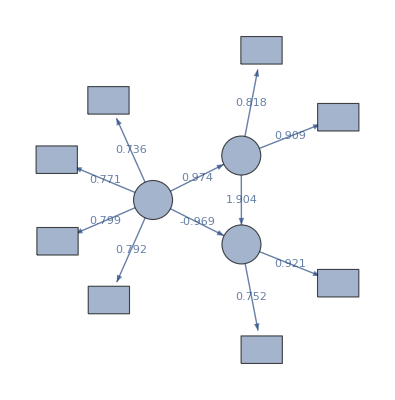

XX->YY 不顯著，以下為完全中介模型

模式配適度

模式配適度指標 | 
卡方值 | 7.271
自由度 | 18.000
P-value | Missing[]
卡方值/自由度 | 0.404
CFI | 1.000
NFI | 0.994
RMSEA | 0.000
GFI | 0.996
AGFI | 0.993

模式配適度Modification Indices值

{}

測量模式與結構模式檢定彙整表

路徑 | 標準化路徑係數 | P-value
XX→X1 | 0.799 | 
XX→X2 | 0.771 | 0.000
XX→X3 | 0.792 | 0.000
XX→X4 | 0.736 | 0.000
MM→M1 | 0.923 | 
MM→M2 | 0.830 | 0.000
YY→Y1 | 0.921 | 
YY→Y2 | 0.752 | 0.000
XX→MM | 0.955 | 0.000
MM→YY | 0.935 | 0.000

研究架構路徑圖

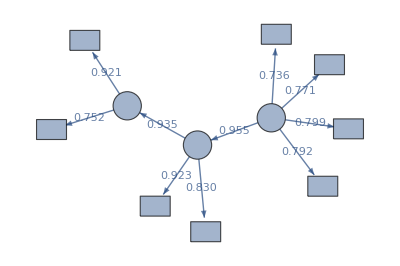

```mathematica
ThesisNoWorryMed[X,M,Y,{3,3,3,3},{3,3},{3,3},{X1,X2,X3,X4},{M1,M2},{Y1,Y2},Dem,DemName,""]
```